# HW 3 - ASTR501 Created with Wolfram Mathematica 11.0 on February 8, 2016

## Daniel George - dgeorge5@illinois.edu

## Q1)

Definition of optical depth τ

```mathematica
sI:=Ι->Ι0 Exp[-τ]
```

Substituting the above in the formula for magnitude difference

```mathematica
Δm -> -2.5 Log10[Ι/Ι0]/.sI//PowerExpand
```

Δm→1.08574 τ

## Q2)

## a)

Substituting quantities in formula for Einstein radius θE

```mathematica
θE->UnitConvert[(√((DAB (Quantity[4, ("GravitationalConstant" "SolarMass")/("SpeedOfLight")^2]))/(DA DB)))Quantity[1, "Radians"]//.{DA->Quantity[8, "Kiloparsecs"],DAB->DA-DB,DB->Quantity[4, "Kiloparsecs"]},Quantity[1, "ArcSeconds"]]
```

θE→0.001009 "

## b)

Since surface brightness (which is flux times solid angle) is conserved

```mathematica
Solve[Subscript[S, obs]==Subscript[S, source]/.{Subscript[S, obs]->Subscript[F, obs]/Subscript[ΔΩ, obs],Subscript[S, source] ->Subscript[F, source]/Subscript[ΔΩ, source]},Subscript[ΔΩ, obs]]
```

{{ΔΩ_obs→(F_obs ΔΩ_source)/F_source}}

Since observed flux is higher than that of source, the subtended solid angle increases.

## Q3)

## a)

Planck function

```mathematica
sB=Bν->2 h ν^3/c^2/(Exp[h ν/(k T)]-1)
```

Bν→(2 h ν^3)/(c^2 (-1+ⅇ^((h ν)/(k T))))

Derivative of B_ν with respect to T

```mathematica
D[Bν/.sB,T]
```

(2 ⅇ^((h ν)/(k T)) h^2 ν^4)/(c^2 (-1+ⅇ^((h ν)/(k T)))^2 k T^2)

Rosseland mean opacity (k_R) definition, using k_ν = j_ν / B_ν

```mathematica
1/Subscript[k, R]==(∫_0^∞ (Bν (∂(Bν))/(∂T))/jν ⅆν)/(∫_0^∞ (∂(Bν))/(∂T)ⅆν)
```

## b)

kν = ke = constant (electron scattering opacity)

Therefore, k_R = k_e from part a)

## Q4)

## a)

Length of the chord traversed by the ray

```mathematica
sd:=d->2(√(-b^2+R^2))
```

Substituting above in the formula for optical depth

```mathematica
sτ=τ->Integrate[α[ν],{x,0,d/.sd}]
```

τ→2 √(-b^2+R^2) α[ν]

## b)

Using the formula for I and setting I_0 to zero and the source function to be the planck function

```mathematica
sΙ=Ι->Ι0 Exp[-τ]+Bν(1-Exp[-τ])/.Ι0->0
```

Ι→Bν (1-ⅇ^-τ)

Integrating I cos(θ) to get flux and setting exp(-τ) to zero in this limit

```mathematica
sF=F->Integrate[Ι Cos[θ]Sin[θ]/.sΙ/.{sB,Exp[-τ]->0},{θ,0,π/2},{ϕ,0,2π},{ν,0,∞},Assumptions->{h>0,k>0,T>0,c>0}]
```

F→(2 k^4 π^5 T^4)/(15 c^2 h^3)

Substituting the above flux to calculate luminosity

```mathematica
L->4π R^2 F/.sF
```

L→(8 k^4 π^6 R^2 T^4)/(15 c^2 h^3)

## c)

Series expansion of the integrand for small τ

```mathematica
int=Normal@Series[Ι Cos[θ]Sin[θ]/.sΙ/.sB,{τ,0,1}]/.sτ/.b->R Sin[θ]
```

(4 h ν^3 Cos[θ] Sin[θ] √(R^2-R^2 Sin[θ]^2) α[ν])/(c^2 (-1+ⅇ^((h ν)/(k T))))

Integrating the above

```mathematica
sF2=F->Integrate[int,{θ,0,π/2},{ϕ,0,2π},{ν,0,∞},Assumptions->{h>0,k>0,T>0,c>0}]
```

F→Integrate[(8 h π √(R^2) ν^3 α[ν])/(3 c^2 (-1+ⅇ^((h ν)/(k T)))),{ν,0,∞},Assumptions→{h>0,k>0,T>0,c>0}]

Luminosity at the above flux

```mathematica
L->4π R^2 F/.sF2
```

L→4 π R^2 Integrate[(8 h π √(R^2) ν^3 α[ν])/(3 c^2 (-1+ⅇ^((h ν)/(k T)))),{ν,0,∞},Assumptions→{h>0,k>0,T>0,c>0}]

Assuming α(ν) is a constant independent of ν, then flux is

```mathematica
sF3=F->(F//.{sF2,α[ν]->α})
```

F→(8 k^4 π^5 √(R^2) T^4 α)/(45 c^2 h^3)

Luminosity at the above flux when α is a constant

```mathematica
L->4π R^2 F/.sF3
```

L→(32 k^4 π^6 (R^2)^(3/2) T^4 α)/(45 c^2 h^3)

## d)

Substituting the expressions for I, Bν, and τ

```mathematica
Iν->Ι/.sΙ/.sτ/.sB
```

Iν→(2 (1-ⅇ^(-2 √(-b^2+R^2) α[ν])) h ν^3)/(c^2 (-1+ⅇ^((h ν)/(k T))))

## e)

Defining function to find ratio of specific intensities:

```mathematica
IRatio[τ_,b_]:=(1-Exp[-τ Sqrt[1-b^2]])/(1-Exp[-τ])
```

Plotting ratio vs b for different τ:

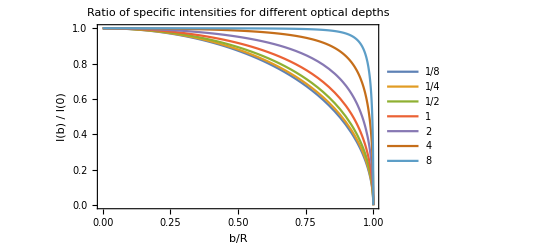

```mathematica
With[{list={1/8,1/4,1/2,1,2,4,8}},Plot[Evaluate@Table[IRatio[τ,b],{τ,list}],{b,0,1},Frame->True,PlotRange->All,PlotLegends->Placed[list,{Left,Center}],FrameLabel->{"b/R","I(b) / I(0)"},PlotLabel->"Ratio of specific intensities for different optical depths",ImageSize->400]]
```

## f)

Integrating the general expression

```mathematica
sF4=F->Integrate[Ι Cos[θ]Sin[θ]//.{sΙ,sB,sτ,b->R Sin[θ]},{θ,0,π/2},{ϕ,0,2π},{ν,0,∞},Assumptions->{h>0,k>0,T>0,c>0}]
```

F→Integrate[(ⅇ^(-2 √(R^2) α[ν]) h π ν^3 (1+2 √(R^2) α[ν]+ⅇ^(2 √(R^2) α[ν]) (-1+2 R^2 α[ν]^2)))/(c^2 (-1+ⅇ^((h ν)/(k T))) R^2 α[ν]^2),{ν,0,∞},Assumptions→{h>0,k>0,T>0,c>0}]

This cannot be simplified further since we do not know α(ν) as a function of ν. If it is a constant then flux is

```mathematica
sF5=sF4/.α[ν]->α//PowerExpand
```

F→(ⅇ^(-2 R α) k^4 π^5 T^4 (1+2 R α+ⅇ^(2 R α) (-1+2 R^2 α^2)))/(15 c^2 h^3 R^2 α^2)

The luminosity is

```mathematica
4π R^2 F/.sF5
```

(4 ⅇ^(-2 R α) k^4 π^6 T^4 (1+2 R α+ⅇ^(2 R α) (-1+2 R^2 α^2)))/(15 c^2 h^3 α^2)

In the limit α → 0, the flux is

```mathematica
Series[F/.sF5,{α,0,1}]
```

(8 k^4 π^5 R T^4 α)/(45 c^2 h^3)+O[α]^2

This is the same flux as part c)

In the limit α → ∞, the flux is

```mathematica
Normal@Series[F/.sF5/.α->1/x,{x,0,1}]/.x->1/α
```

(2 k^4 π^5 T^4)/(15 c^2 h^3)+(2 ⅇ^(-2 R α) k^4 π^5 T^4)/(15 c^2 h^3 R α)

The second term is zero in the limit as exp(-α) → 0 as α → ∞. Therefore this is the same flux as part b)

Therefore the limits match.